```mathematica
SetDirectory[NotebookDirectory[]];
Nc=3.;
mf2[h_,ρ_]:=(h^2 ρ)/2;
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
F1[q_,ρ_,h_,T_,μ_]:=q^2/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^2/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^2 NIntegrate[(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,500.,5000.},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
(*gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5])-(Nc h^2 mf2[h,ρ])/(16 π^2);*)
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2*(-2+Log[mf2[h,ρ]/MZ^2]+(√(4 mf2[h,ρ]+(p0^2+ps^2)) Log[((√(p0^2+ps^2))+√(4 mf2[h,ρ]+(p0^2+ps^2)^2))/(-(√(p0^2+ps^2))+√(4 mf2[h,ρ]+(p0^2+ps^2)^2))])/(√(p0^2+ps^2))))-(Nc h^2 mf2[h,ρ])/(16 π^2);
gamma2[p0_,ps_,ρ_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ];
λ300=75.8;
ν300=-482.^2;
```

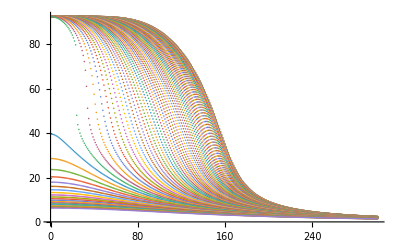

```mathematica
sigmadata=Import["../sigma0.dat"];
ListPlot[sigmadata]
```

```mathematica
muq=Table[i*5,{i,1,80}];
muq[[64]]
sigmadata[[64]][[30]]
```

320

18.0133

## M values

```mathematica
fixM1=ParallelTable[gamma2[0.,p,(sigmadata[[64]][[30]])^2/2,6.5,30.,320.,√(300.^2),√(300.^2)]+(p)^2+(λ300 (sigmadata[[64]][[30]])^2/2+ν300),{p,1,1000,10}];
```

$Aborted

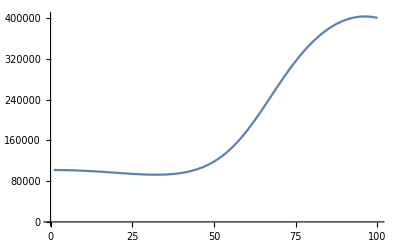

```mathematica
ListLinePlot[fixM1]
```

```mathematica
Mp=ParallelTable[gamma2[0.,p,(sigmadata[[64]][[30]])^2/2,6.5,30.,320.,√(300.^2),√(300.^2+(p^2))]+(p)^2+(λ300 (sigmadata[[64]][[30]])^2/2+ν300),{p,1,1000,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Mp2=ParallelTable[gamma2[0.,p,(sigmadata[[64]][[30]])^2/2,6.5,30.,320.,√(300.^2),√(300.^2+(2 p^2))]+(p)^2+(λ300 (sigmadata[[64]][[30]])^2/2+ν300),{p,1,1000,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ps=Table[i*10,{i,1,100}];
```

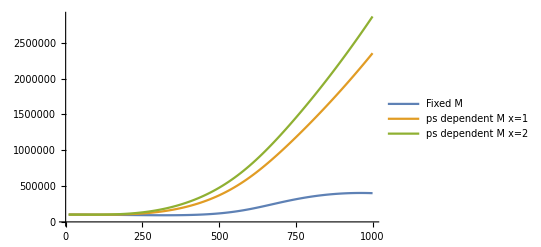

```mathematica
ListLinePlot[{Transpose[{ps,fixM}],Transpose[{ps,Mp}],Transpose[{ps,Mp2}]},PlotLegends->{"Fixed M","ps dependent M x=1","ps dependent M x=2"}]
```

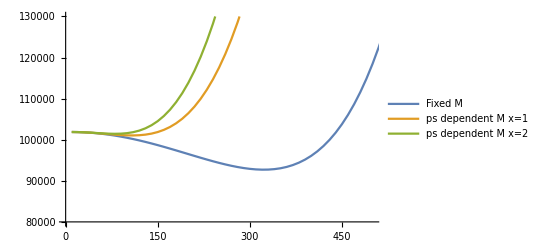

```mathematica
ListLinePlot[{Transpose[{ps,fixM}],Transpose[{ps,Mp}],Transpose[{ps,Mp2}]},PlotRange->{{0,500},{80000,130000}},PlotLegends->{"Fixed M","ps dependent M x=1","ps dependent M x=2"}]
```

## High T (CA effect)

```mathematica
T300mu0=ParallelTable[gamma2[0.,p,(sigmadata[[1]][[300]])^2/2,6.5,300.,0.,√(300.^2),√(300.^2)]+(p)^2+(λ300 (sigmadata[[1]][[300]])^2/2+ν300),{p,1,1000,10}];
```

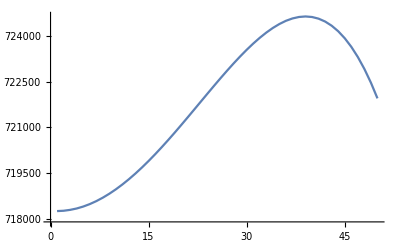

```mathematica
ListLinePlot[T300mu0[[1;;50]]]
```